# Tutorial #2:

## Sums, Series, Special Functions

Start the Tutorial by opening up the “Template” document from Blackboard.

Last time, we covered:

```mathematica
h[x_]:=x^2 Cos[x]
D[h[x],x]
Integrate[h[x],{x,0,2π}]
Plot[{h[x],Evaluate[D[h[x],x]]},{x,-10,10}]
```

Remember:

4 Basic Rules :

Capital letters on all command names.

[ ] surround function arguments.

Eg. f[x]:=Sin[x]/x

Note: There is a difference between using = vs. := for definitions

{ } are use for lists and ranges.

Shift + Enter to evaluate input (or Enter on your number pad).

? brings up the manual entry for a command

Blue is undefined, black is defined.

Warmup: Plot:

```mathematica
f[n_,k_,x_]:=((-1)^k(x/2)^(n+2k))/(k!Gamma[n+k+1])
```

For k = 0, 1, 2 and n = 0 on 0<x<10

## Replacement Rules and Sums

Replacement rules allow us to make substitutions in our functions and expressions. A full form Replace[ ] is available, but we often use the shorthand postscript notation at the end of an expression.
i.e.

```mathematica
(Gamma[x]+x^2)/Cos[x]/.x->5
Cos[x]/.x->{0,π/2,π,3 π/2,2π}
y^2 Cos[x*y]/.{y->x}
```

49 Sec[5]

{1,0,-1,0,1}

x^2 Cos[x^2]

Exercise: Use replacement rules to redo the warm-up for k=0, 1, 2, 3, 4, 5 (with n=0).

Exercise: Define a function h(x,m) that is the sum of f(n,x) on k∈[0, m], k∈Integers. (with n=0)
Plot h(x,1), h(x,10), h(x, ∞) (don’t use replacement rules this time).
Evaluate h(x, ∞) on its own. What do you notice?

## Series

Series uses the same syntax as Sum, only it performs a power series expansion. Take a look at the documentation and see for detail. When manipulating Series, you may need to use the Normal[ ] command to truncate.

a+a^3/3+(2 a^5)/15+O[a]^6

a+a^3/3+(2 a^5)/15

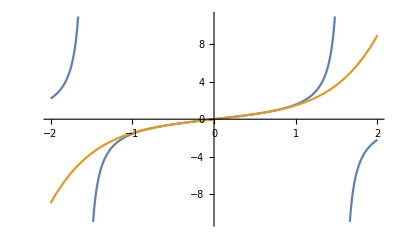

```mathematica
Series[Tan[a],{a,0,5}]
Normal[Series[Tan[a],{a,0,5}]]
Plot[
{Tan[a],Evaluate[Normal[Series[Tan[a],{a,0,5}]]]},
{a,-2,2}]
```

Exercise: Define a function g(a, n) which is the series expansion about x=0 of the cosine function of argument a up to order n, i.e. 
		g[a_, n_]:=Series[Cos[a],{a,0,n}]
Test this out for a few values of n. Investigate the Normal command, then plot g(a,1), g(a,3), g(a,5), and cos(a) all on the same plot with legends, axes labels, and a title. Note: you will have to wrap each function g(a,n) inside of an Evaluate[ ] command when plotting.

## Introduction to Solving Equations

There’s lots of ways to solve equations using Mathematica:

```mathematica
?Solve
?NSolve
?Reduce
?FindRoot
```

RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to solve the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"]}], "]"}] solves over the domain StyleBox["dom", "TI"]. Common choices of StyleBox["dom", "TI"] are Reals, Integers, and Complexes.

RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to find numerical approximations to the solutions of the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", "Reals"}], "]"}] finds solutions over the domain of real numbers.

RowBox[{"Reduce", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] reduces the statement StyleBox["expr", "TI"] by solving equations or inequalities for StyleBox["vars", "TI"] and eliminating quantifiers. 
RowBox[{"Reduce", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"]}], "]"}] does the reduction over the domain StyleBox["dom", "TI"]. Common choices of StyleBox["dom", "TI"] are Reals, Integers, and Complexes.

RowBox[{"FindRoot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}]}], "]"}] searches for a numerical root of StyleBox["f", "TI"], starting from the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}].
RowBox[{"FindRoot", "[", RowBox[{RowBox[{StyleBox["lhs", "TI"], "==", StyleBox["rhs", "TI"]}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}]}], "]"}] searches for a numerical solution to the equation RowBox[{StyleBox["lhs", "TI"], "==", StyleBox["rhs", "TI"]}]. 
RowBox[{"FindRoot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a simultaneous numerical root of all the SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].
RowBox[{"FindRoot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["eqn", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["eqn", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a numerical solution to the simultaneous equations SubscriptBox[StyleBox["eqn", "TI"], StyleBox["i", "TI"]].

For most realistic cases, we'll use the FindRoot[ ] command, which deals with input numerically. Whenever we deal with solving numerical equations, wherever possible it's beneficial to plot your functions first to inspect any problematic regions (asymptotes, multiple solutions, etc)

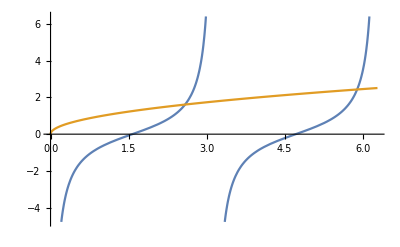

```mathematica
Plot[{-Cot[z],Sqrt[z]},{z,0,2π}]
FindRoot[-Cot[z]==Sqrt[z],{z,5}]
```

Exercise: Find the smallest positive solution for tan(x) = √(z_0^2/z^2-1)

Reminder: Include name in Mathematica notebook, with a filename lastnamefirstinitial_Tutorial2.nb (eg. HoJ_Tutorial2.nb) and email the completed notebook to j.ho@example.ca